```mathematica
GetSnapshot[n_]:=ReadList["/Users/nicorivas/Software/BOS2/BOS/build/snapsot_"<>ToString[n]<>".dat",{Number,Number,Number}]
```

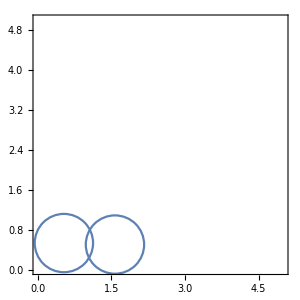
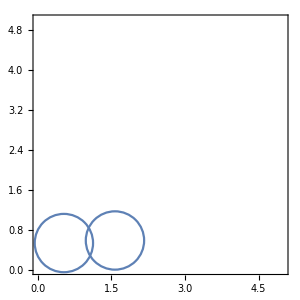

```mathematica
Row[{ListPlot[GetSnapshot[1][[All,{1,3}]],PlotRange->{{0,5},{0,5}},Frame->True,AspectRatio->1,ImageSize->300,PlotMarkers->Graphics[Circle[],ImageSize->300/5*0.5*2]],ListPlot[GetSnapshot[1][[All,{1,2}]],PlotRange->{{0,5},{0,5}},Frame->True,AspectRatio->1,ImageSize->300,PlotMarkers->Graphics[Circle[],ImageSize->300/5*0.5*2]]}]
```